```mathematica
d[p_]:=(Sqrt[p]/2+Sqrt[p/4+1])^(-2)
```

```mathematica
sol =DSolve[{d[p] n''[r]-Sqrt[p d[p]]n'[r]-n[r]/c==Exp[-r],n[0]==1/2},n[r],r];
```

```mathematica
Collect[n[r]/.sol,{ⅇ^(1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))-√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)) r),ⅇ^(1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))+√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)) r)}]
```

{(ⅇ^-r (4 c+2 c p+2 c √p √(4+p)))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(ⅇ^(-r+1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))+√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)) r) (-2 ⅇ^r-2 c ⅇ^r-ⅇ^r p-2 c ⅇ^r p-ⅇ^r √p √(4+p)-2 c ⅇ^r √p √(4+p)+4 c ⅇ^r √(p/(√p+√(4+p))^2)+2 c ⅇ^r p √(p/(√p+√(4+p))^2)+2 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2)+4 ⅇ^r C[1]-4 c ⅇ^r C[1]+2 ⅇ^r p C[1]+2 ⅇ^r √p √(4+p) C[1]-8 c ⅇ^r √(p/(√p+√(4+p))^2) C[1]-4 c ⅇ^r p √(p/(√p+√(4+p))^2) C[1]-4 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2) C[1]))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(ⅇ^(-r+1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))-√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)) r) (-4 ⅇ^r C[1]+4 c ⅇ^r C[1]-2 ⅇ^r p C[1]-2 ⅇ^r √p √(4+p) C[1]+8 c ⅇ^r √(p/(√p+√(4+p))^2) C[1]+4 c ⅇ^r p √(p/(√p+√(4+p))^2) C[1]+4 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2) C[1]))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))}

```mathematica
Manipulate[Plot[{1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))-√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)),1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))+√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2))},{p,0,10}],{c,0.01,10}]
```

```mathematica
Solve[(e^(-r)(-2 ⅇ^r-2 c ⅇ^r-ⅇ^r p-2 c ⅇ^r p-ⅇ^r √p √(4+p)-2 c ⅇ^r √p √(4+p)+4 c ⅇ^r √(p/(√p+√(4+p))^2)+2 c ⅇ^r p √(p/(√p+√(4+p))^2)+2 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2)+4 ⅇ^r C[1]-4 c ⅇ^r C[1]+2 ⅇ^r p C[1]+2 ⅇ^r √p √(4+p) C[1]-8 c ⅇ^r √(p/(√p+√(4+p))^2) C[1]-4 c ⅇ^r p √(p/(√p+√(4+p))^2) C[1]-4 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2) C[1]))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))==0,C[1]]
```

{{C[1]→((e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(c e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r p)/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(c e^-r ⅇ^r p)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r √p √(4+p))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(c e^-r ⅇ^r √p √(4+p))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(c e^-r ⅇ^r p √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(c e^-r ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))/((2 e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r p)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r √p √(4+p))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(4 c e^-r ⅇ^r √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r p √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))}}

```mathematica
FullSimplify[((e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(c e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r p)/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(c e^-r ⅇ^r p)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r √p √(4+p))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))+(c e^-r ⅇ^r √p √(4+p))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(c e^-r ⅇ^r p √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(c e^-r ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))/((2 e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r p)/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))+(e^-r ⅇ^r √p √(4+p))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(4 c e^-r ⅇ^r √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r p √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))-(2 c e^-r ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2))/(-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))),Assumptions->r>0&&p>0&&c>0]
```

(1+c)/(2-2 c)

```mathematica
(*The negative sign root is always negative, and the positive sign root is always positive. Demanding lim_(r->Infty) n_t[r]->0 gives the integration constant (1+c)/(2-2 c)*)
```

```mathematica
f[r_,p_,c_,d_]:=(ⅇ^(-r+1/2 (√(p/(√p+√(4+p))^2) (2+p+√p √(4+p))-√(-(2 (-2-p-√p √(4+p)))/c+(p (2+p+√p √(4+p))^2)/(√p+√(4+p))^2)) r) (-4 ⅇ^r d+4 c ⅇ^r d-2 ⅇ^r p d-2 ⅇ^r √p √(4+p) d+8 c ⅇ^r √(p/(√p+√(4+p))^2) d+4 c ⅇ^r p √(p/(√p+√(4+p))^2) d+4 c ⅇ^r √p √(4+p) √(p/(√p+√(4+p))^2) d))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2)))
```

```mathematica
FullSimplify[f[r,p,c,(1+c)/(2-2 c)],Assumptions->c>0&&p>0&&r>0]
```

-((1+c) ⅇ^(1/4 (p+√(p (4+p))-√2 √(((4+c p) (2+p+√(p (4+p))))/c)) r))/(2 (-1+c))

```mathematica
FullSimplify[(ⅇ^-r (4 c+2 c p+2 c √p √(4+p)))/(2 (-2+2 c-p-√p √(4+p)+4 c √(p/(√p+√(4+p))^2)+2 c p √(p/(√p+√(4+p))^2)+2 c √p √(4+p) √(p/(√p+√(4+p))^2))),Assumptions->c>0&&p>0&&r>0]
```

(c ⅇ^-r)/(-1+c)

```mathematica
n[r_,p_,c_]:=(c ⅇ^-r)/(-1+c) -((1+c) ⅇ^(1/4 (p+√(p (4+p))-√2 √(((4+c p) (2+p+√(p (4+p))))/c)) r))/(2 (-1+c))
```

```mathematica
Manipulate[Plot[{n[r,p,c],Exp[-r]/2},{r,0,10},PlotRange->Full],{p,0,10},{c,0.01,10}]
```

```mathematica
FullSimplify[n[0,p,c],Assumptions->p>0&&c>0]
```

c/(-1+c)-(2 (-1+c) (1+c) (√(4+p)+√p (3+p+√(p (4+p))))^2)/(√p+√(4+p))^2

```mathematica
DSolve[d r''[t]- r'[t]-2 r[t]/3==0,r[t],t]
```

{{r[t]→ⅇ^(1/2 (1/d-(√(3+8 d))/(√3 d)) t) C[1]+ⅇ^(1/2 (1/d+(√(3+8 d))/(√3 d)) t) C[2]}}

```mathematica
Integrate[(1-m^2)/(m (1+m^2)),m]
```

Log[m]-Log[1+m^2]

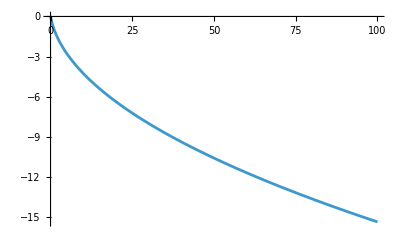

```mathematica
Plot[(1-(√(3+8 d))/(√3)),{d,0,100}]
```

```mathematica
Solve[M^3-3M+2x==0,M,Assumptions->x>0]
```

{{M→1/((-x+√(-1+x^2))^(1/3))+(-x+√(-1+x^2))^(1/3)},{M→-(1+ⅈ √3)/(2 (-x+√(-1+x^2))^(1/3))-1/2 (1-ⅈ √3) (-x+√(-1+x^2))^(1/3)},{M→-(1-ⅈ √3)/(2 (-x+√(-1+x^2))^(1/3))-1/2 (1+ⅈ √3) (-x+√(-1+x^2))^(1/3)}}

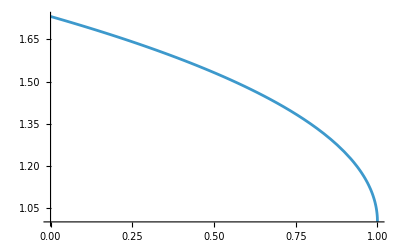

```mathematica
Plot[1/((-x+√(-1+x^2))^(1/3))+(-x+√(-1+x^2))^(1/3),{x,0,1}]
```